# Principal Component Analysis

## 3D feature space analysis with PCA

### Create random point cloud and rotate it randomly

```mathematica
SeedRandom[0];
```

```mathematica
{θ1,θ2,θ3}={RandomReal[{0,2π}],RandomReal[{0,2π}],RandomReal[{0,2π}]};
randomRotM={{Cos[θ1],-Sin[θ1],0},{Sin[θ1],Cos[θ1],0},{0,0,1}}.{{1,0,0},{0,Cos[θ2],-Sin[θ2]},{0,Sin[θ2],Cos[θ2]}}.{{Cos[θ3],-Sin[θ3],0},{Sin[θ3],Cos[θ3],0},{0,0,1}};
pts={};
For[i=1,i≤500,i++,
{r1,r2,r3}={RandomReal[{-10,10}],RandomReal[{-4,4}],RandomReal[{-1,1}]};
{θ,ϕ}={RandomReal[{0,2π}],RandomReal[{0,π}]};
res=randomRotM.{r1 Cos[θ] Sin[ϕ],r2 Sin[θ] Sin[ϕ],r3 Cos[ϕ]};
res=randomRotM.{r1,r2,r3};
AppendTo[pts,res];
];
```

### Find Cluster centers and shift to zero mean

```mathematica
ptsCenter=Plus@@pts/Length[pts];
```

```mathematica
ptsS=Table[pts[[i]]-ptsCenter,{i,Length[pts]}];
```

```mathematica
ptsS1=Table[{-10,ptsS[[i,2]],ptsS[[i,3]]},{i,Length[ptsS]}];
ptsS2=Table[{ptsS[[i,1]],10,ptsS[[i,3]]},{i,Length[ptsS]}];
ptsS3=Table[{ptsS[[i,1]],ptsS[[i,2]],-10},{i,Length[ptsS]}];
p2=ListPointPlot3D[{ptsS,ptsS1,ptsS2,ptsS3},PlotRange->{{-10,10},{-10,10},{-10,10}},Boxed->True,AspectRatio->1,Ticks->None]
```

-Graphics3D-

### Compute covariance matrix

```mathematica
CMat=Transpose[ptsS].ptsS;
CMat//MatrixForm
```

(8860.81 | 386.229 | 7623.73
386.229 | 2089.94 | -874.529
7623.73 | -874.529 | 7616.9)

### Compute Eigensystem of covariance matrix

```mathematica
{eigVal,OMat}=Eigensystem[CMat];
Print["Eigenvalues: ", MatrixForm[eigVal],"; Eigenvectors: ", MatrixForm[OMat]];
```

Eigenvalues: (15894.8
2509.31
163.496); Eigenvectors: (0.734208 | -0.0224444 | 0.678554
0.304258 | 0.904348 | -0.2993
-0.606931 | 0.426204 | 0.670809)

### Perform basis change into eigendirections

```mathematica
ptsSR=Table[ptsS[[i]].Transpose[OMat],{i,Length[ptsS]}];
```

### Plot rotated points and their projections along the three coordinate axes

```mathematica
p1=ListPointPlot3D[ptsSR,AspectRatio->1,Filling->Bottom,PlotRange->{{-10,10},{-10,10},{-10,10}},Ticks->None];
```

```mathematica
ptsSRP1=Table[{-10,ptsSR[[i,2]],ptsSR[[i,3]]},{i,Length[ptsSR]}];
ptsSRP2=Table[{ptsSR[[i,1]],10,ptsSR[[i,3]]},{i,Length[ptsSR]}];
ptsSRP3=Table[{ptsSR[[i,1]],ptsSR[[i,2]],-10},{i,Length[ptsSR]}];
p2=ListPointPlot3D[{ptsSRP1,ptsSRP1,ptsSRP2,ptsSRP3},Ticks->None,PlotRange->{{-10,10},{-10,10},{-10,10}}];
```

```mathematica
Show[{p1,p2}]
```

-Graphics3D-

### Compute the maximum variance explained and make a Scree plot (not very useful in this case)

```mathematica
maxvarexp=eigVal/Plus@@eigVal
```

{0.85605,0.135144,0.00880543}

#### Individual MVE

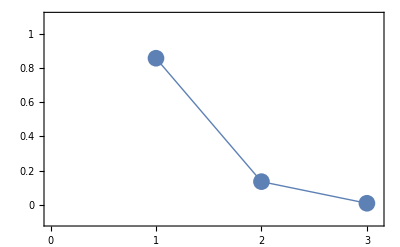

```mathematica
Show[
ListPlot[maxvarexp,PlotStyle->PointSize[0.03],Frame->{True,True,False,False},
FrameTicks->{{{0,0.2,0.4,0.6,0.8,1},None},{{0,1,2,3},None}},FrameTicksStyle->Directive[20],PlotRange->{{0,3.1},{-0.1,1.1}}],
Graphics[{Thick,ColorData[97,"ColorList"][[1]],Line[Table[{i,maxvarexp[[i]]},{i,Length[maxvarexp]}]]}]
]
```

#### Summed MVE

```mathematica
maxvarexpSummed=Table[Sum [maxvarexp[[i]],{i,1,j}],{j,3}]
```

{0.85605,0.991195,1.}

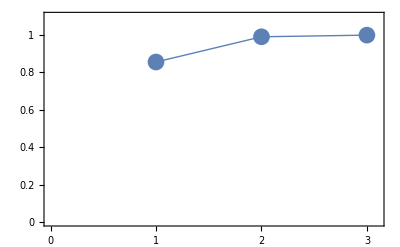

```mathematica
Show[
ListPlot[maxvarexpSummed,PlotStyle->PointSize[0.03],Frame->{True,True,False,False},
FrameTicks->{{{0,0.2,0.4,0.6,0.8,1},None},{{0,1,2,3},None}},FrameTicksStyle->Directive[20],PlotRange->{{0,3.1},{0,1.1}}],
Graphics[{Thick,ColorData[97,"ColorList"][[1]],Line[Table[{i,maxvarexpSummed[[i]]},{i,Length[maxvarexpSummed]}]]}]
]
```

## 8D feature space analysis with PCA

### Create random point cloud and rotate it randomly

```mathematica
SeedRandom[0];
```

```mathematica
pts={};
For[i=1,i≤5000,i++,
{r1,r2,r3,r4,r5,r6,r7,r8}={RandomReal[{-25,25}],RandomReal[{-20,20}],RandomReal[{-15,15}],RandomReal[{-10,10}],RandomReal[{-5,5}],RandomReal[{-1,1}],RandomReal[{-0.5,0.5}],RandomReal[{-0.1,0.1}]};
res={r1,r2,r3,r4,r5,r6,r7,r8};
AppendTo[pts,res];
];
```

### Find Cluster centers and shift to zero mean

```mathematica
ptsCenter=Plus@@pts/Length[pts];
```

```mathematica
ptsS=Table[pts[[i]]-ptsCenter,{i,Length[pts]}];
```

### Compute covariance matrix

```mathematica
CMat=Transpose[ptsS].ptsS;
CMat//MatrixForm
```

(1.03816×10^6 | -15162.8 | 5171.95 | -4513.48 | -2216.26 | 776.427 | -591.275 | -30.4869
-15162.8 | 665283. | 4581.62 | 2002.94 | -966.758 | -247.576 | -113.284 | 98.8834
5171.95 | 4581.62 | 372647. | 525.192 | -3154.03 | 183.14 | -100.392 | 14.8989
-4513.48 | 2002.94 | 525.192 | 165212. | 2162.98 | 21.8625 | 81.8723 | -9.6878
-2216.26 | -966.758 | -3154.03 | 2162.98 | 41588.1 | -46.1818 | -55.1817 | -4.19995
776.427 | -247.576 | 183.14 | 21.8625 | -46.1818 | 1654.56 | 6.26212 | -0.335051
-591.275 | -113.284 | -100.392 | 81.8723 | -55.1817 | 6.26212 | 416.278 | -0.574469
-30.4869 | 98.8834 | 14.8989 | -9.6878 | -4.19995 | -0.335051 | -0.574469 | 16.8801)

### Compute Eigensystem of covariance matrix

```mathematica
{eigVal,OMat}=Eigensystem[CMat];
Print["Eigenvalues: ", MatrixForm[eigVal],"; Eigenvectors: ", MatrixForm[OMat]];
```

Eigenvalues: (1.03885×10^6
664755.
372562.
165218.
41514.2
1653.79
415.737
16.8622); Eigenvectors: (0.999135 | -0.0404853 | 0.00748486 | -0.0052557 | -0.00221626 | 0.000758908 | -0.0005655 | -0.0000330103
0.040374 | 0.999042 | 0.01641 | 0.00365048 | -0.00176381 | -0.000320955 | -0.000208178 | 0.000147087
-0.00815134 | -0.0161183 | 0.999789 | 0.00245587 | -0.00940985 | 0.000488666 | -0.000249908 | 0.0000364147
-0.00516187 | 0.00379296 | 0.00231038 | -0.999824 | -0.0174884 | -0.000156379 | -0.000476351 | 0.00006251
0.00211901 | 0.00158673 | 0.00949587 | -0.01747 | 0.999797 | -0.00109313 | -0.00143544 | -0.0000914488
-0.000736732 | 0.00036259 | -0.000476763 | -0.000174191 | 0.00110348 | 0.999985 | 0.00535703 | -0.000177077
-0.000575877 | -0.000183412 | -0.000274847 | 0.000502102 | -0.00141682 | 0.00535844 | -0.999983 | 0.00142677
0.0000285477 | -0.000147462 | -0.000037542 | 0.0000593544 | 0.0000952693 | 0.000169394 | 0.00142761 | 0.999999)

### Perform basis change into eigendirections

```mathematica
ptsSR=Table[ptsS[[i]].Transpose[OMat],{i,Length[ptsS]}];
```

### Compute the maximum variance explained and make a Scree plot (not very useful in this case)

#### Individual MVE

```mathematica
maxvarexp=eigVal/Plus@@eigVal
```

{0.454641,0.290923,0.163048,0.0723059,0.0181683,0.000723763,0.000181943,7.3796×10^-6}

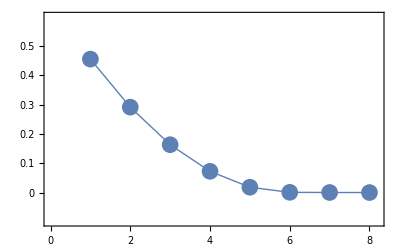

```mathematica
Show[
ListPlot[maxvarexp,PlotStyle->PointSize[0.03],
Frame->{True,True,False,False},
FrameTicks->{{{0,0.1,0.2,0.3,0.4,0.5},None},{{0,1,2,3,4,5,6,7,8},None}},FrameTicksStyle->Directive[20],PlotRange->{{0,8.2},{-0.1,0.6}}],
Graphics[{Thick,ColorData[97,"ColorList"][[1]],Line[Table[{i,maxvarexp[[i]]},{i,Length[maxvarexp]}]]}]
]
```

#### Summed MVE

```mathematica
maxvarexpSummed=Table[Sum [maxvarexp[[i]],{i,1,j}],{j,Length[maxvarexp]}]
```

{0.454641,0.745565,0.908613,0.980919,0.999087,0.999811,0.999993,1.}

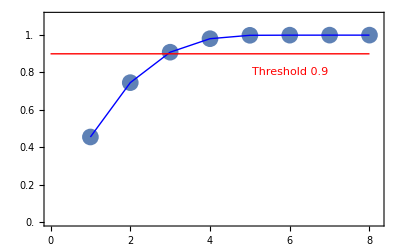

```mathematica
Show[ListPlot[maxvarexpSummed,PlotStyle->PointSize[0.03],
Frame->{True,True,False,False},
FrameTicks->{{Table[i,{i,0,1,0.1}],None},{{0,1,2,3,4,5,6,7,8},None}},FrameTicksStyle->Directive[20],PlotRange->{{0,8.2},{0,1.1}}],
Graphics[{Thick, Blue,Line[Table[{i,maxvarexpSummed[[i]]},{i,Length[maxvarexpSummed]}]]}],
Graphics[{Thick, Red,Line[{{0,0.9},{8,0.9}}]}],
Graphics[{Thick, Red,Style[Text["Threshold 0.9",{6,0.8}],FontSize->18]}]
]
```